```mathematica
(*Parameters*)
L=1;
Hp=0.2;
param=1;
Npt=100;

(*Chebyshev grid and first/second derivative matrices*)
chebPoints=Reverse@Table[Cos[π i/Npt],{i,0,Npt}];
xGrid=L*chebPoints;
(*ListPlot[Transpose[{xGrid,chebPoints}]]*)
```

```mathematica
(*Chebyshev differentiation matrices*)
T=Table[Cos[π i j/Npt],{i,0,Npt},{j,0,Npt}]; (*DCT matrix*)
c=Join[{2},Table[1,{Npt-1}],{2}];
D1=ConstantArray[0,{Npt+1,Npt+1}];

For[i=1,i<=Npt+1,i++,For[j=1,j<=Npt+1,j++,If[i!=j,D1[[i,j]]=(c[[i]]/c[[j]])*(-1)^(i+j)/(xGrid[[i]]-xGrid[[j]]);,If[i==1,D1[[i,j]]=(2 Npt^2+1)/6;,If[i==Npt+1,D1[[i,j]]=-(2 Npt^2+1)/6;,D1[[i,j]]=0;];];];]];

D1=D1/L;
D2=D1.D1;
```

```mathematica
(*Define H0(x)*)
(*H0vals=Hp (1-(xGrid/L)^2);*)
H0vals=Hp*Exp[-(xGrid/2/(L/6))^2];

(*Now define the matrices*)
H0col=H0vals; (*just the function values*)
(*H0mat=Table[H0col,{Npt+1}]//Transpose;*)
H0mat = DiagonalMatrix[H0col];

(*Operator A=D H0 D*)
A=D1.H0mat.D1;

(*Operator B=H0 D^2 H0 (carefully interpreted)*)
B=-param*(H0mat.D2.H0mat);

(*(*Apply Dirichlet/Neumann BCs at endpoints*)*)
interior=Range[2,Npt];(*indices of interior grid points*)

Aint=A;
Bint=B;
Aint[[1]]=Join[{1},ConstantArray[0,Npt]];
(*Aint[[1]]=D1[[1]];
Bint[[1]]=ConstantArray[0,Npt+1];*)
Aint[[Npt+1]]=D1[[Npt+1]];
Bint[[Npt+1]]=ConstantArray[0,Npt+1];
```

```mathematica
(*Solve eigenvalue problem B v=σ A v*)
{sigmaVals,eigVecs}=Eigensystem[{Bint,Aint},6];
sigmaVals
```

{-179.848,-88.7138,-0.216473,-0.201104,-0.199107,-0.195117}

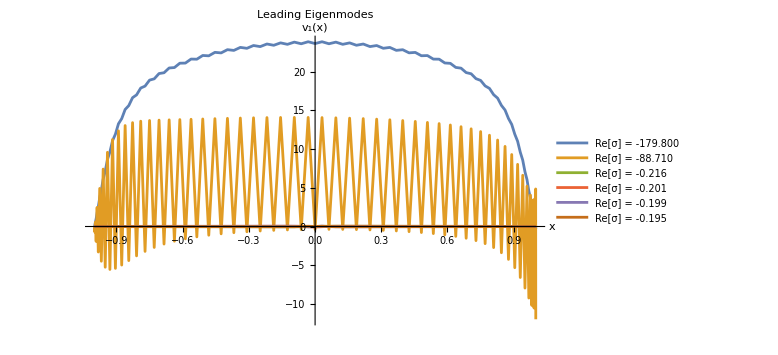

```mathematica
(*Normalize and plot*)
normVecs=Normalize/@eigVecs;

ListLinePlot[Table[Transpose@{xGrid,sigmaVals[[i]]*normVecs[[i]]},{i,1,Length[normVecs]}],PlotLabel->"Leading Eigenmodes",PlotLegends->Placed[LineLegend[Table[Row[{"Re[σ] = ",NumberForm[Re[sigmaVals[[i]]],{4,3}]}],{i,Length[sigmaVals]}]],Below],AxesLabel->{"x","v₁(x)"},ImageSize->Large,PlotRange->Full]
```

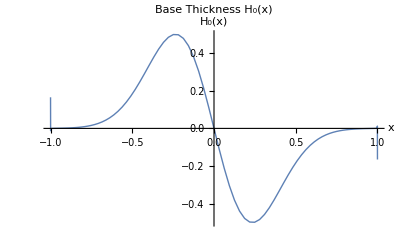

```mathematica
ListLinePlot[Transpose[{xGrid,(D1.H0vals)}],AxesLabel->{"x","H₀(x)"},PlotLabel->"Base Thickness H₀(x)",PlotStyle->Thick]
```

```mathematica
(*MatrixPlot[H0mat,ColorFunction->"ThermometerColors",Frame->True,PlotLegends->Automatic]*)
```